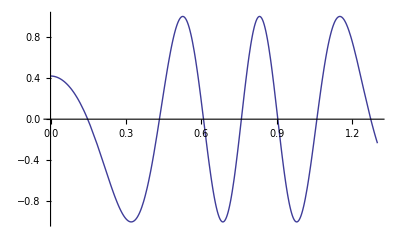

```mathematica
f[x_]:=Sin[5*x^4-20x^2+13]
Plot[f[x],{x,0,1.3}]
```

```mathematica
(* Metoda prostokatow *)
MetodaProstokatow[xmin_,xmax_,n_]:=Block[{h=(xmax-xmin)/n,S=0},
For[i=0,i<n,i++,xi=xmin+i h;S=S+h f[xi]];
Return[N[S]]];
```

```mathematica
(* Metoda trapezow *)
MetodaTrapezow[xmin_,xmax_,n_]:=Block[{h=(xmax-xmin)/n,S=0},
For[i=0,i<n,i++,xi=xmin+i h;xii=xmin+(i+1)h;
S=S+h(f[xi]+f[xii])/2];
Return[N[S]]];
```

```mathematica
(*Metoda Simpsona *)
MetodaSimpsona[xmin_,xmax_,n_]:=Block[{h=(xmax-xmin)/n,S=0},
For[i=0,i<n,i=i+2,xi=xmin+i h;xii=xmin+(i+1)h;
xiii=xmin+(i+2)h;S=S+h(f[xi]+4f[xii]+f[xiii])/3];
Return[N[S]]];
```

```mathematica
(*Metoda Monte Carlo *)
MetodaMonteCarlo[xmin_,xmax_,ymin_,ymax_,n_]:=Block[{P=(xmax-xmin)(ymax-ymin),Pm=(xmax-xmin)ymin,l=0},
For[i=0,i<n,i++,xi=xmin+Random[Real,xmax-xmin];
yi=ymin+Random[Real,ymax-ymin];If[yi<f[xi],l++]];
S=l P/n+Pm;
Return[N[S]]];
```

```mathematica
NIntegrate[f[x],{x,0,1.3}]
```

0.00717163

```mathematica
xmin=0;
xmax=1.3;
ymin=-1;
ymax=1;
w1=Table[MetodaProstokatow[xmin,xmax,n],{n,1,25}];
w2=Table[MetodaTrapezow[xmin,xmax,n],{n,1,25}];
w3=Table[MetodaSimpsona[xmin,xmax,n],{n,1,25}];
w4=Table[MetodaMonteCarlo[xmin,xmax,ymin,ymax,10000],{n,1,25}];
```

```mathematica
Print[w1];
Print[w2];
Print[w3];
Print[w4];
```

{0.546217,-0.211193,0.494256,-0.754196,0.188746,0.0759492,0.0389365,0.0434051,0.0407782,0.038619,0.0366724,0.0349139,0.0333279,0.0318962,0.0306011,0.0294265,0.028358,0.0273828,0.0264901,0.0256704,0.0249154,0.0242181,0.0235723,0.0229726,0.0224145}

{0.12093,-0.423837,0.352493,-0.860518,0.103689,0.00506796,-0.0218189,-0.00975579,-0.00647593,-0.00390974,-0.00199008,-0.00052674,0.000613432,0.00151848,0.00224863,0.00284608,0.00334109,0.00375577,0.00410659,0.00440602,0.00466362,0.00488683,0.00508151,0.00525232,0.00540302}

{-0.441361,-0.605426,0.000818139,-1.00608,-0.0310814,-0.11074,-0.0772554,0.273832,-0.211047,-0.0397759,-0.00254122,-0.00239164,-0.0473711,0.0092976,-0.0347015,0.00704671,-0.0280325,0.00716633,-0.0231821,0.00717794,-0.0193581,0.00717913,-0.0163054,0.00717868,-0.0138235}

{-0.0039,-0.00078,0.0104,-0.026,-0.01144,0.01092,2.22045×10^-16,0.0273,0.00026,0.00884,-0.0078,-0.01144,0.01508,0.03172,0.02444,0.01534,0.02158,0.0117,0.00234,0.02418,0.00494,0.0156,-0.0078,0.02548,0.01118}

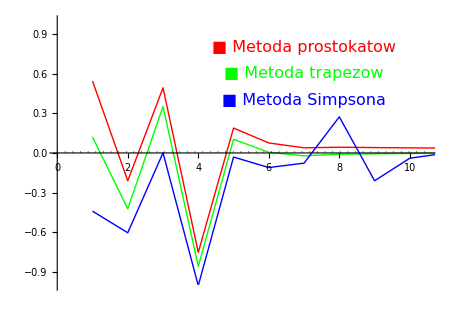

```mathematica
Show[ListLinePlot[w1,PlotRange->{{0,10.5},{-1,1}},PlotStyle->Red,AspectRatio->0.7],
ListLinePlot[w2,PlotRange->{{0,10.5},{-1,1}},PlotStyle->Green,AspectRatio->0.7],
ListLinePlot[w3,PlotRange->{{0,10.5},{-1,1}},PlotStyle->Blue,AspectRatio->0.7],
Plot[0.007171630135348172,{x,0,10.5},PlotStyle->{Black,Dotted,Thick}],
Epilog->{Inset[Style["■ Metoda prostokatow",Red,16],{7,0.8}],Inset[Style["■ Metoda trapezow",Green,16],{7,0.6}],Inset[Style["■ Metoda Simpsona",Blue,16],{7,0.4}]}
]
```

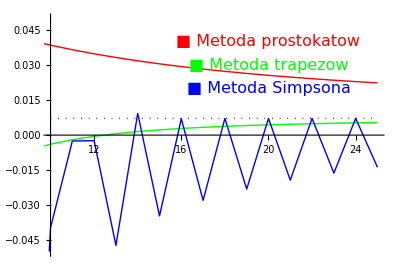

```mathematica
Show[ListLinePlot[w1,PlotRange->{{10,25},{-0.05,0.05}},PlotStyle->Red,AspectRatio->0.7],
ListLinePlot[w2,PlotRange->{{10,25},{-0.05,0.05}},PlotStyle->Green,AspectRatio->0.7],
ListLinePlot[w3,PlotRange->{{10,25},{-0.05,0.05}},PlotStyle->Blue,AspectRatio->0.7],
Plot[0.007171630135348172,{x,10,25},PlotStyle->{Black,Dotted,Thick}],
Epilog->{Inset[Style["■ Metoda prostokatow",Red,16],{20,0.04}],Inset[Style["■ Metoda trapezow",Green,16],{20,0.03}],Inset[Style["■ Metoda Simpsona",Blue,16],{20,0.02}]}
]
```

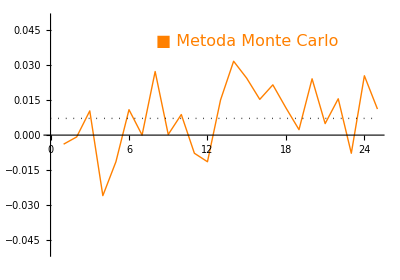

```mathematica
Show[ListLinePlot[w4,PlotRange->{{0,25},{-0.05,0.05}},PlotStyle->Orange,AspectRatio->0.7],
Plot[0.007171630135348172,{x,0,25},PlotStyle->{Black,Dotted,Thick}],
Epilog->{Inset[Style["■ Metoda Monte Carlo",Orange,16],{15,0.04}]}
]
```